# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\All models comparison

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
Clear[haar];
haar[dim_Integer]:=Module[{l=2^dim,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
(*Define the Lipkin Hamiltonian*)
Clear[Hlmg];
Hlmg[α_,gx_,gy_,n_]:=α*Jz[n]+(gx/(n-1))(Jx[n].Jx[n])+(gy/(n-1))(Jy[n].Jy[n]);
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

### Ensemble of initial states ψ_s ⊗ ψ_e, Chaotic

# Wisniacki chain

## Chaotic

```mathematica
L=6;
hx=J=1.;
hz=0.5;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=100;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTb=Table[Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψb=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTb},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
ope2=Jz[L].Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
vara=Table[Chop[Conjugate[ψa[[i]]].ope2.ψa[[i]]]-maga[[i]],{i,Length[ψa]}];
varb=Table[Chop[Conjugate[ψb[[i]]].ope2.ψb[[i]]]-magb[[i]],{i,Length[ψb]}];
varc=Table[Chop[Conjugate[ψc[[i]]].ope2.ψc[[i]]]-magc[[i]],{i,Length[ψc]}];
```

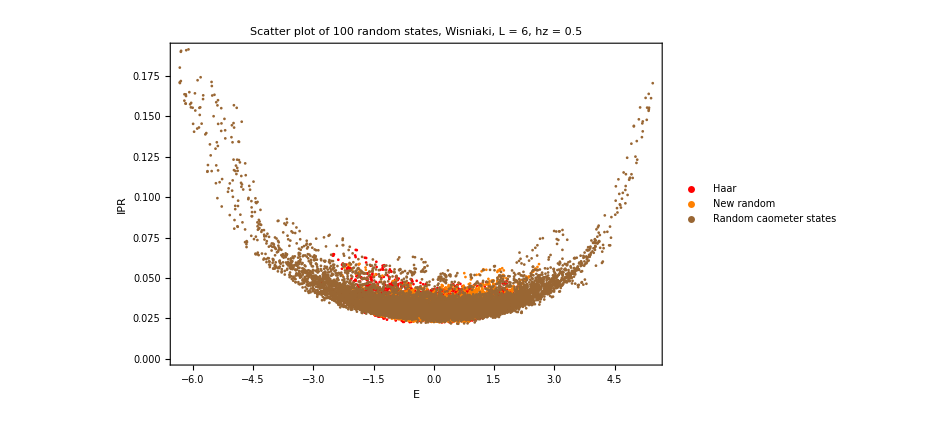

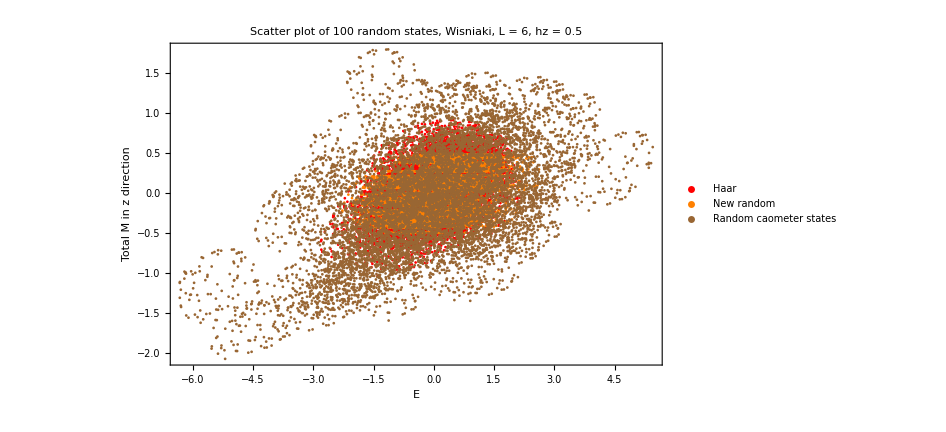

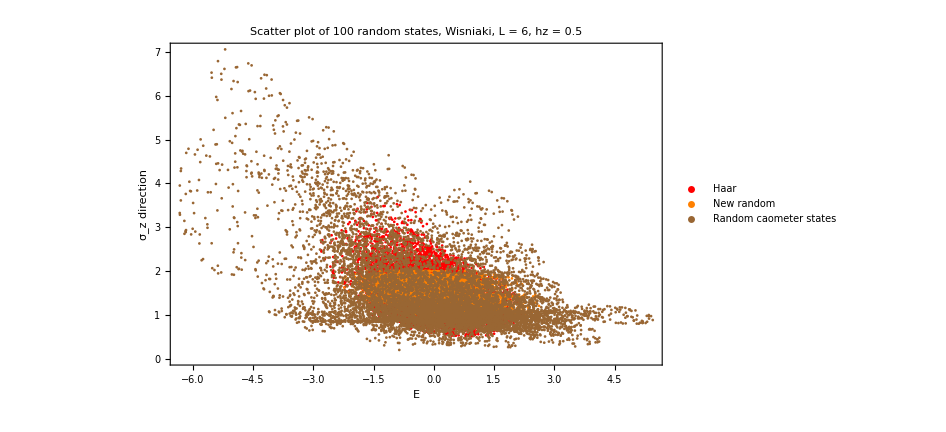

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,vara}],Transpose[{energiesb,varb}],Transpose[{energiesc,varc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["σ_z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

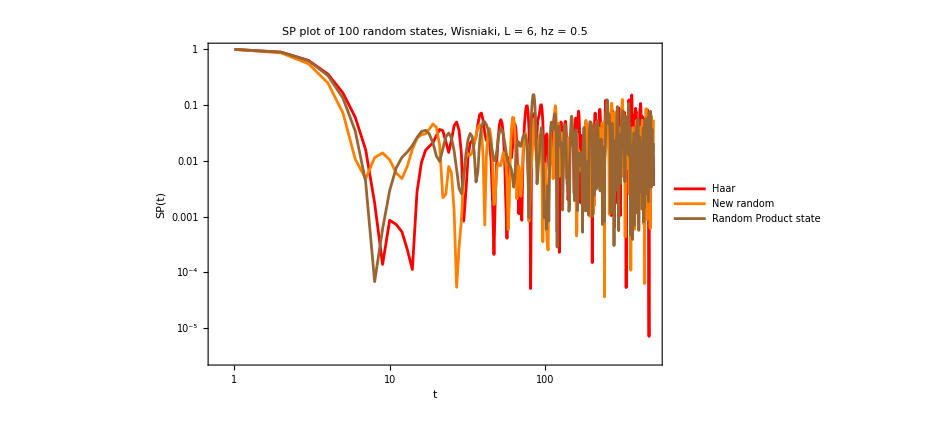

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

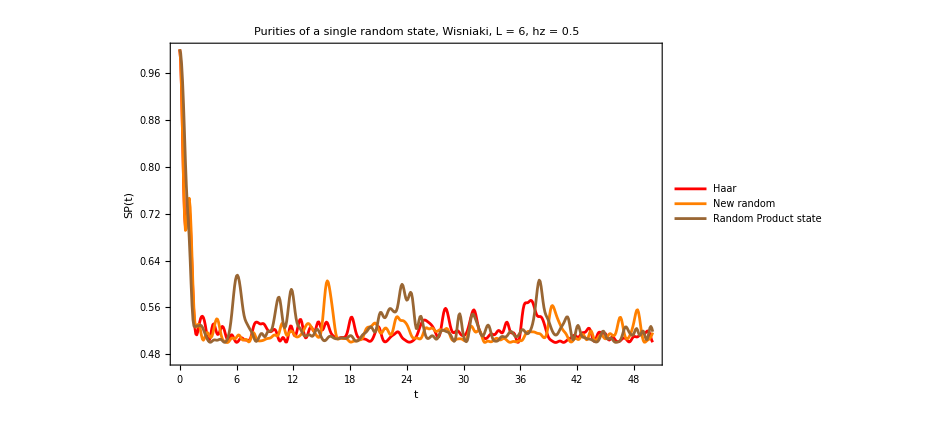

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

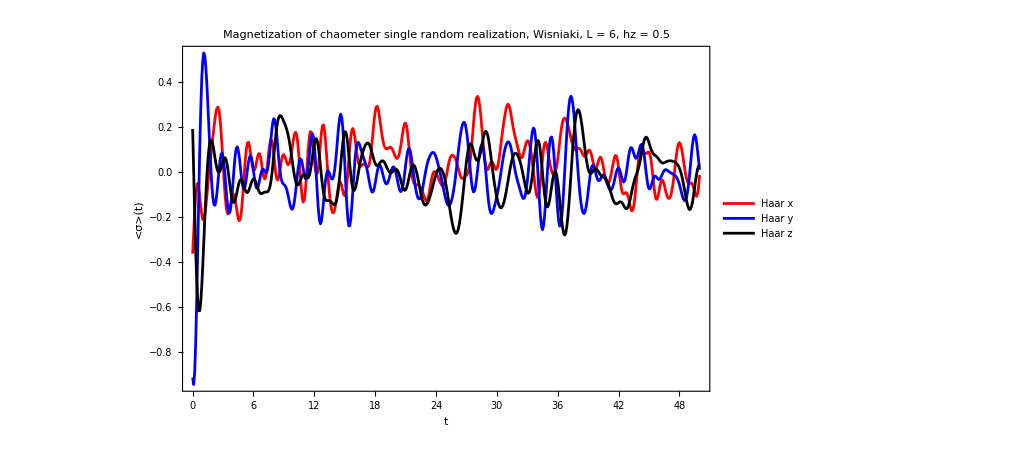

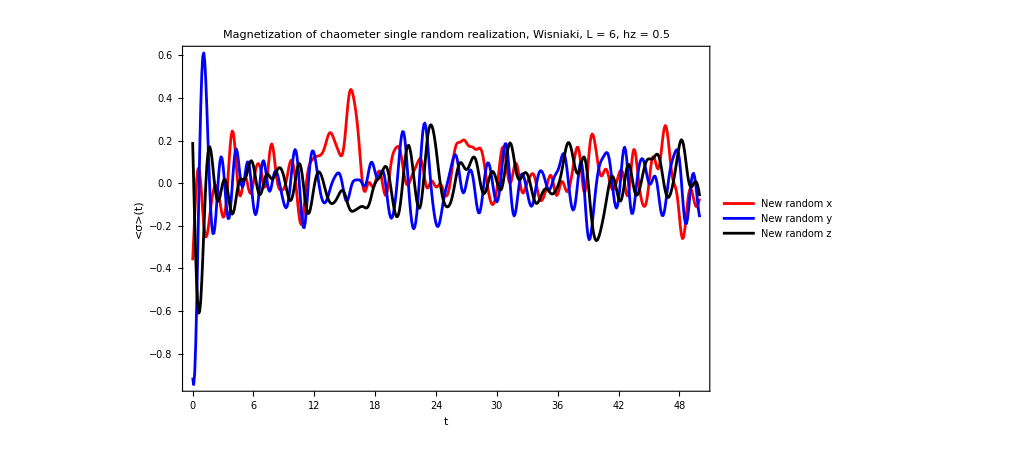

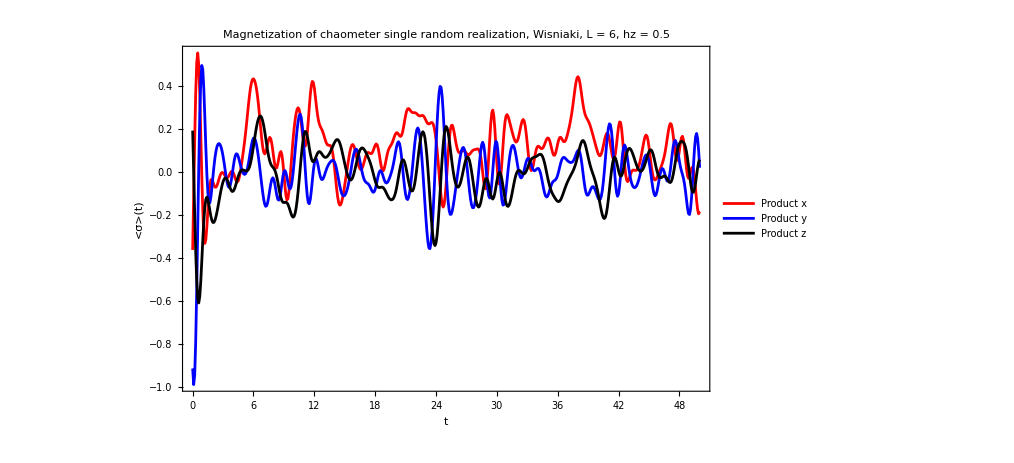

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

## Regular

```mathematica
L=5;
hx=J=1.;
hz=4.0;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
caometer=Table[haar[1],{i,50}];
```

```mathematica
ψa=Table[Flatten[KroneckerProduct[i,haar[L-1]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,RandomChainProductState[L-1]]],{i,caometer}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
```

```mathematica
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
```

```mathematica
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
```

```mathematica
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
```

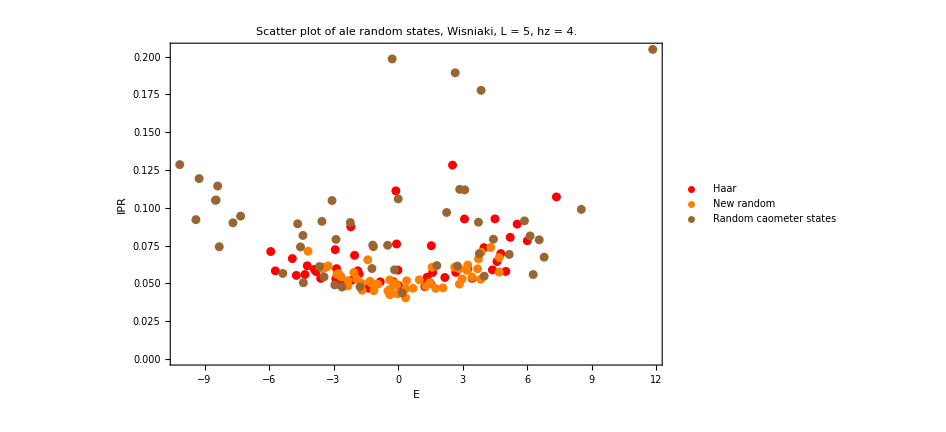

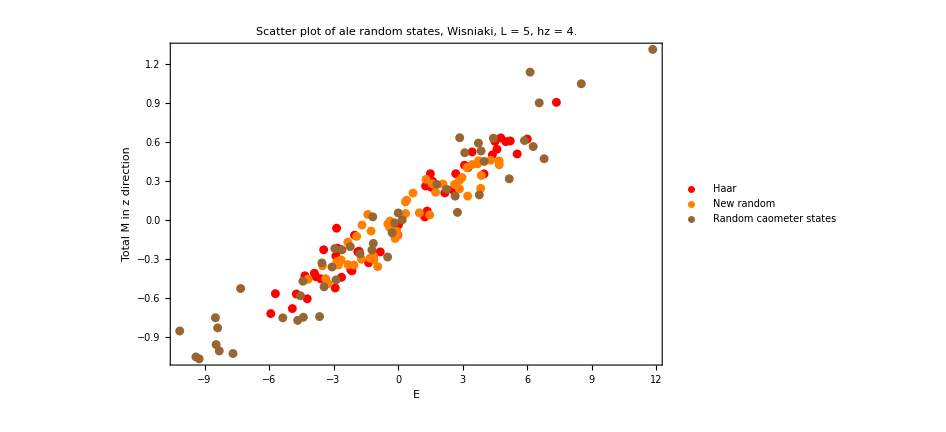

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

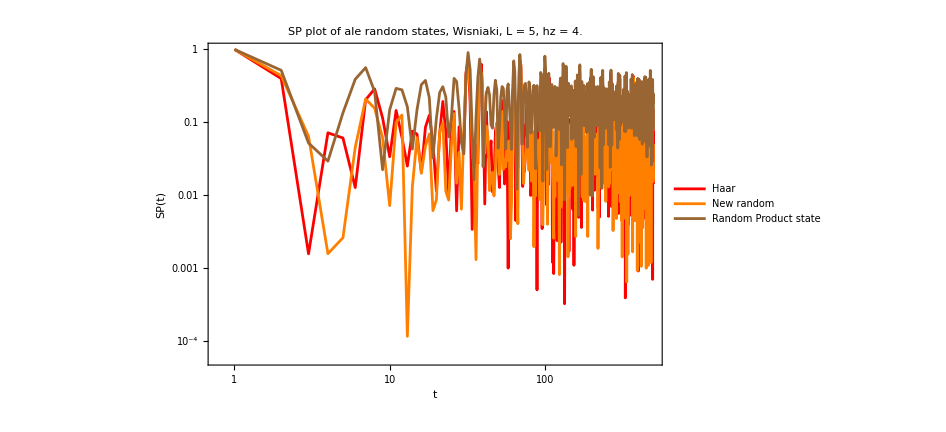

```mathematica
ListLogLogPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
```

```mathematica
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
```

```mathematica
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,50,0.1];
```

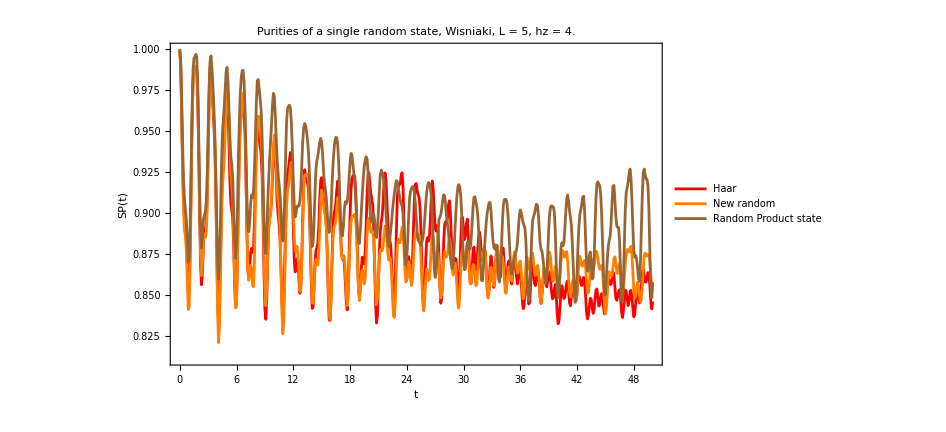

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]},PlotRange->All]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

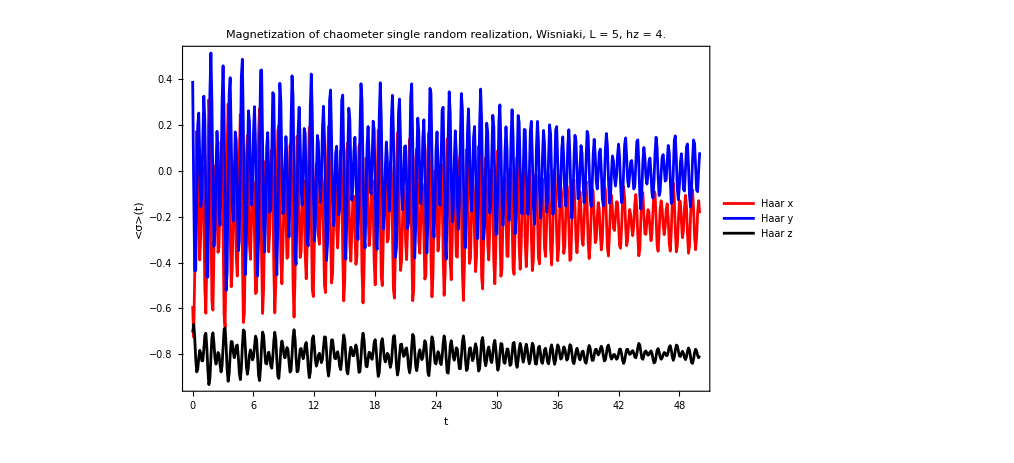

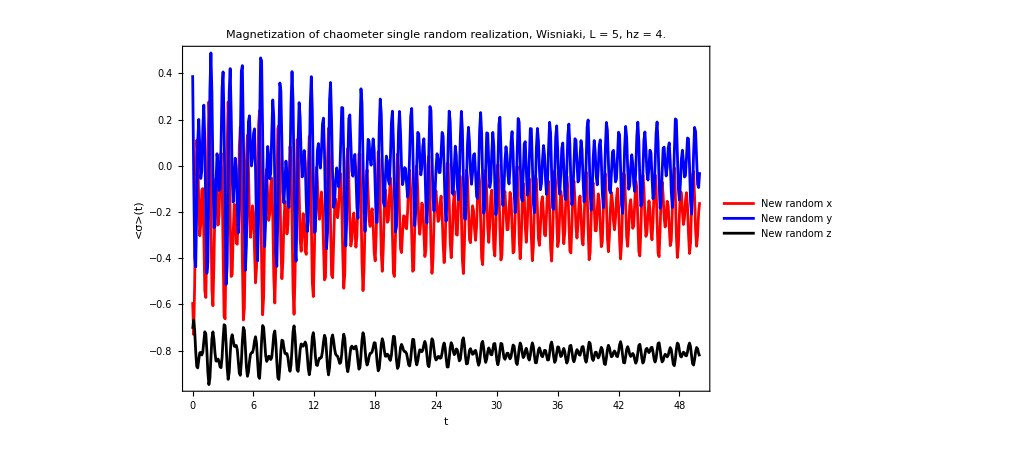

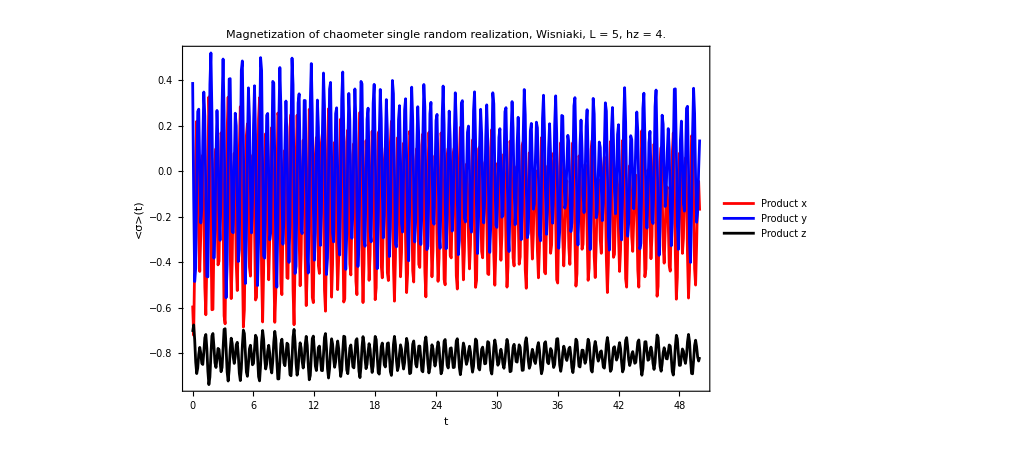

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Magnetization of chaometer single random realization, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Directive[Red],Directive[Blue],Directive[Black]},ImageSize->750,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product z",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]},PlotRange->All]
```

## Quantum channel

```mathematica
?Superoperator
```

```mathematica
L=6;
hx=J=1.;
hz=4.;
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ψe=RandomChainProductState[L-1];
```

```mathematica
tlist=Range[0,10,0.1];
```

```mathematica
superop=Table[Superoperator[t,ψe,eigenval,eigenvec,L],{t,tlist}];
```

```mathematica
choimat=ParallelTable[1/2.Reshuffle[i],{i,superop}];
```

```mathematica
eigenvals=Table[Chop[Eigenvalues[i]],{i,choimat}];
```

```mathematica
eigenvals//Dimensions
```

{101,4}

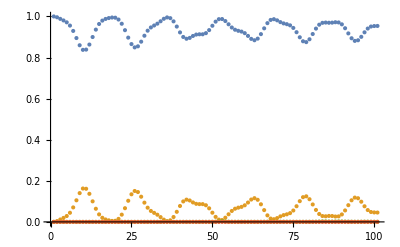

```mathematica
ListPlot[Transpose[eigenvals]]
```

# XXZ Chain

```mathematica
L=7;
Δ=1.;
H=ClosedXXZHamiltonian[L,Δ];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
```

```mathematica
ale=2;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTb=Table[Normalize[Table[Exp[i*I*RandomReal[]],{i,2^(L-1)}]],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψb=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTb},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
ope=Jz[L];
ope2=Jz[L].Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
vara=Table[Chop[Conjugate[ψa[[i]]].ope2.ψa[[i]]]-maga[[i]],{i,Length[ψa]}];
varb=Table[Chop[Conjugate[ψb[[i]]].ope2.ψb[[i]]]-magb[[i]],{i,Length[ψb]}];
varc=Table[Chop[Conjugate[ψc[[i]]].ope2.ψc[[i]]]-magc[[i]],{i,Length[ψc]}];
```

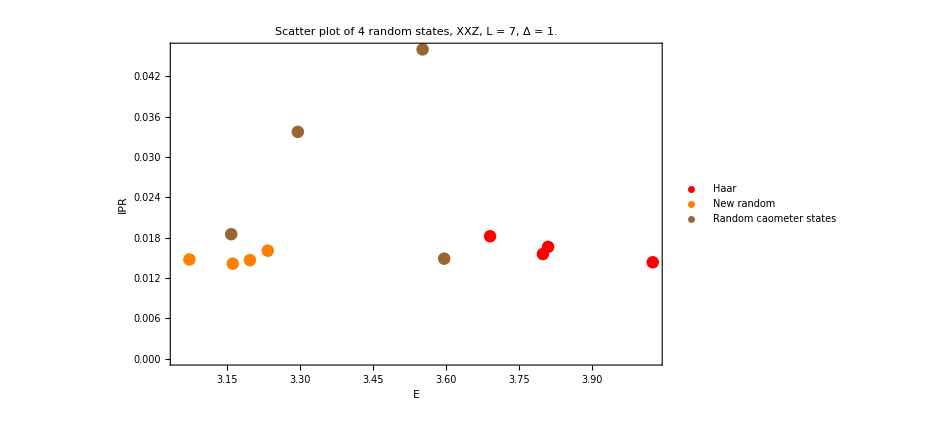

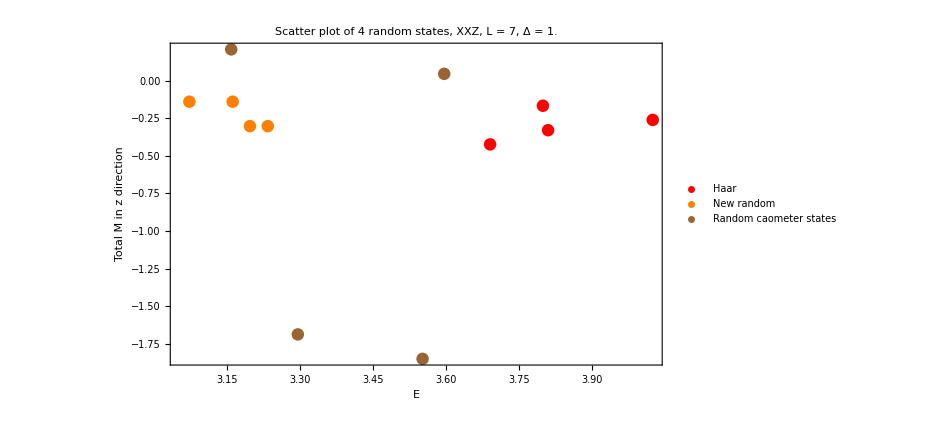

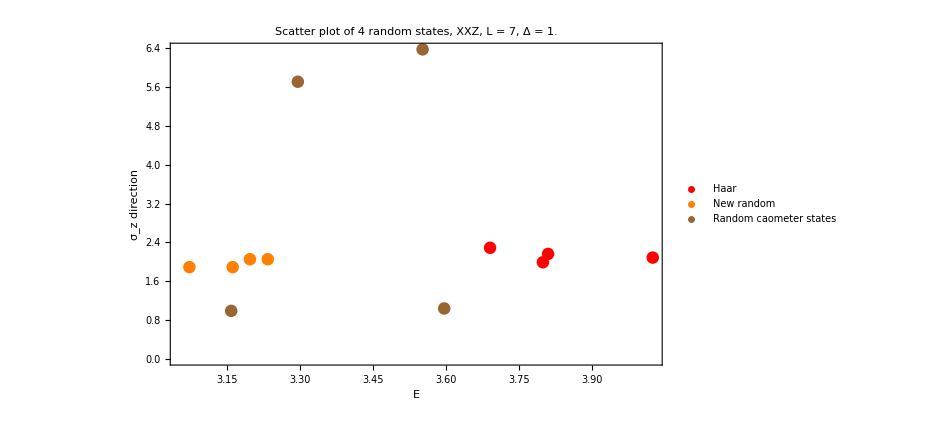

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale*ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale*ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,vara}],Transpose[{energiesb,varb}],Transpose[{energiesc,varc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale*ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random caometer states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["σ_z direction"]}]
```

```mathematica
tf=50.0;
ψat=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψa[[1;;10]]},{t,0,tf,0.1}];
ψbt=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψb[[1;;10]]},{t,0,tf,0.1}];
ψct=Table[StateEvolution[t,j,eigenval,eigenvec],{j,ψc[[1;;10]]},{t,0,tf,0.1}];
```

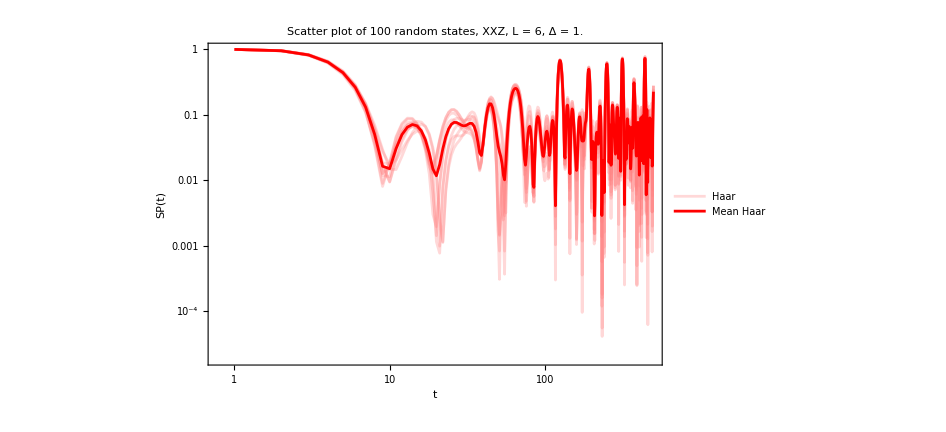

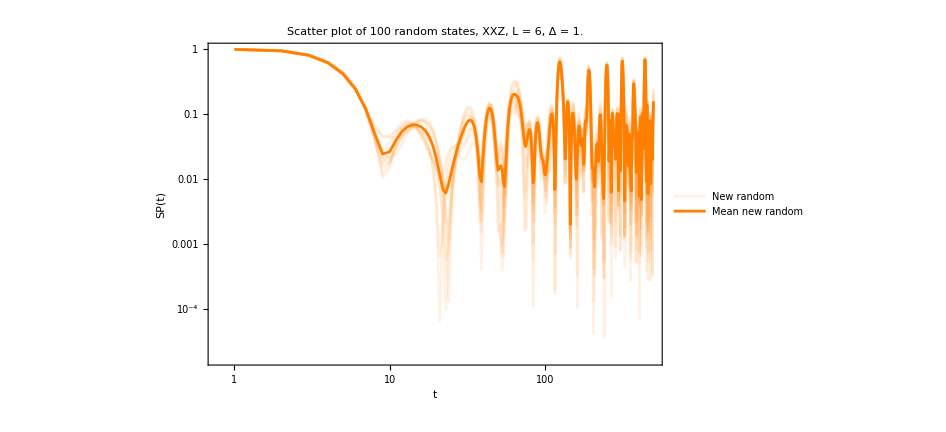

```mathematica
singlea=ListLogLogPlot[Table[Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2,{j,Length[ψat]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Pink,Opacity[0.3]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meana=ListLogLogPlot[Mean[Table[Abs[Conjugate[ψat[[j,1]]].ψat[[j,i]]]^2,{j,Length[ψat]},{i,Length[Range[0,tf,0.1]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Red,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean Haar",Red]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
singleb=ListLogLogPlot[Table[Abs[Conjugate[ψbt[[j,1]]].ψbt[[j,i]]]^2,{j,Length[ψbt]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Orange,Opacity[0.1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["New random",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meanb=ListLogLogPlot[Mean[Table[Abs[Conjugate[ψbt[[j,1]]].ψbt[[j,i]]]^2,{j,Length[ψbt]},{i,Length[Range[0,tf,0.1]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Orange,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean new random",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
Show[{singlea,meana}]
Show[{singleb,meanb}]
```

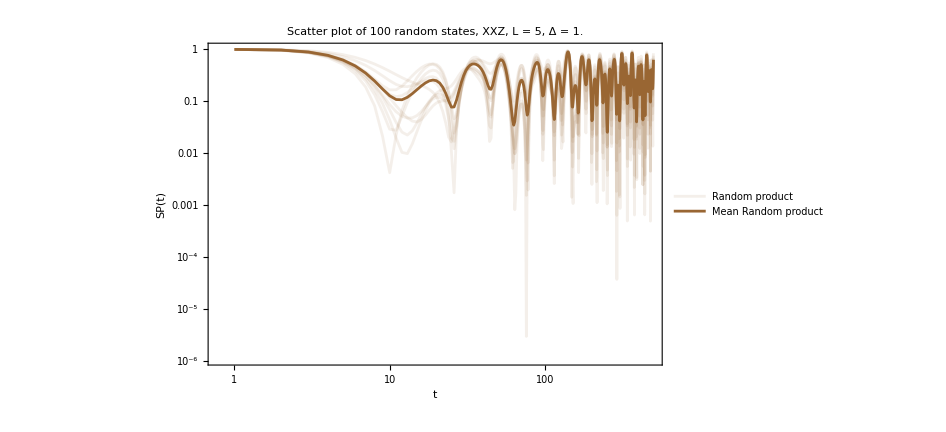

```mathematica
singlec=ListLogLogPlot[Table[Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2,{j,Length[ψct]},{i,Length[Range[0,tf,0.1]]}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown,Opacity[0.1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
meanc=ListLogLogPlot[Mean[Table[Abs[Conjugate[ψct[[j,1]]].ψct[[j,i]]]^2,{j,Length[ψbt]},{i,Length[Range[0,tf,0.1]]}]],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Directive[Brown,Opacity[1]]},PlotRange->All,ImageSize->700,PlotLegends->{Style["Mean Random product",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}];
Show[{singlec,meanc}]
```

```mathematica
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,50,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,50,0.1}];
```

```mathematica
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=Table[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

```mathematica
tlist=Range[0,tf,0.1];
```

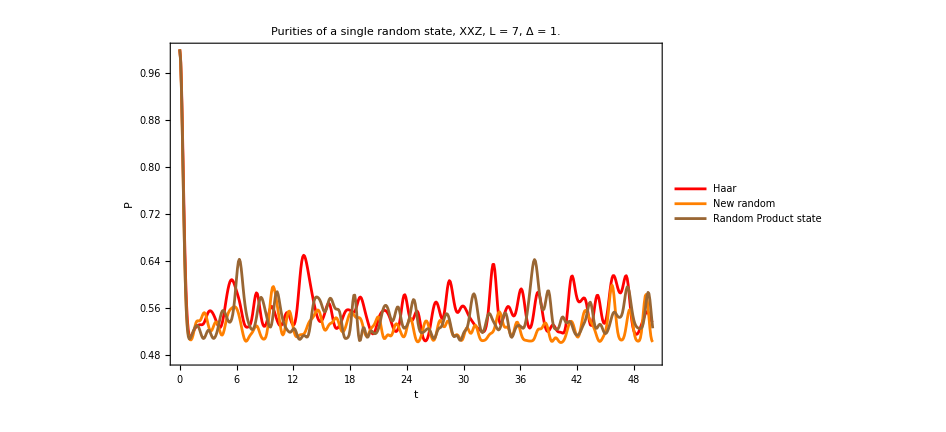

```mathematica
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmagax=Table[Chop[Tr[sx.i]],{i,reduceda}];
reducedmagay=Table[Chop[Tr[sy.i]],{i,reduceda}];
reducedmagaz=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagbx=Table[Chop[Tr[sx.i]],{i,reducedb}];
reducedmagby=Table[Chop[Tr[sy.i]],{i,reducedb}];
reducedmagbz=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagcx=Table[Chop[Tr[sx.i]],{i,reducedc}];
reducedmagcy=Table[Chop[Tr[sy.i]],{i,reducedc}];
reducedmagcz=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

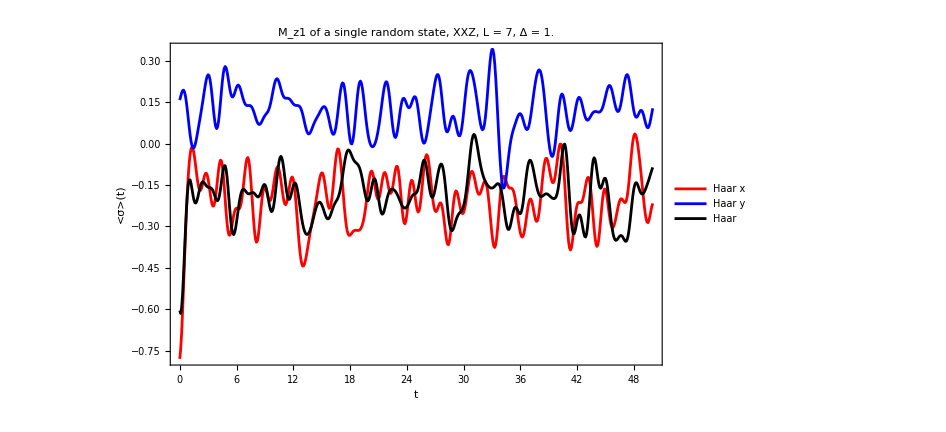

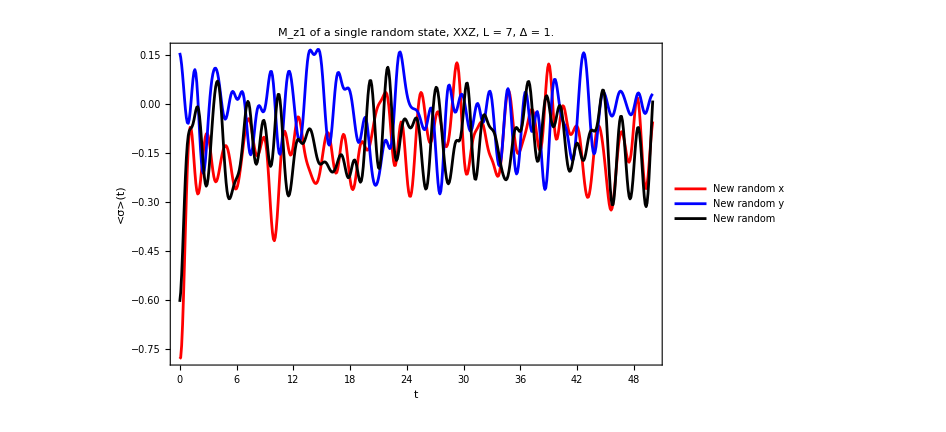

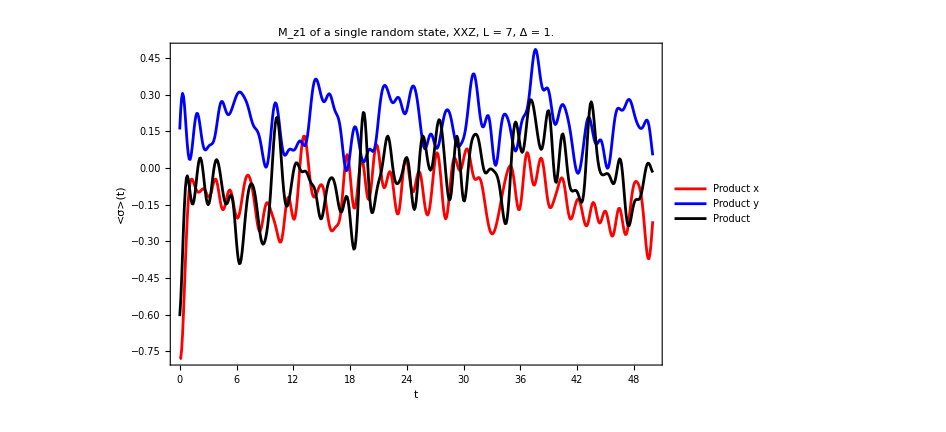

```mathematica
ListPlot[{Transpose[{tlist,reducedmagax}],Transpose[{tlist,reducedmagay}],Transpose[{tlist,reducedmagaz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar x",Red],Style["Haar y",Blue],Style["Haar ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]

ListPlot[{Transpose[{tlist,reducedmagbx}],Transpose[{tlist,reducedmagby}],Transpose[{tlist,reducedmagbz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["New random x",Red],Style["New random y",Blue],Style["New random ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]

ListPlot[{Transpose[{tlist,reducedmagcx}],Transpose[{tlist,reducedmagcy}],Transpose[{tlist,reducedmagcz}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, XXZ, L = "<>ToString[L]<>", Δ = "<>ToString[Δ]<>"",20,Black],PlotStyle->{Red,Blue,Black},PlotRange->All,ImageSize->700,PlotLegends->{Style["Product x",Red],Style["Product y",Blue],Style["Product ",Black]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["<σ>(t)"]}]
```

# LMG model

```mathematica
L=6;
α=1.;
gx=0.43;
gy=0.57;
H=Hlmg[α,gx,gy,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
eigenvec=Orthogonalize[eigenvec];
```

```mathematica
ale=100;
caometer=Table[haar[1],{i,ale}];
ψTa=Table[haar[L-1],{i,ale}];
ψTc=Table[RandomChainProductState[L-1],{i,ale}];
```

```mathematica
ψa=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTa},{i,caometer}],{ale*ale,2^L}];
ψc=ArrayReshape[ParallelTable[Flatten[KroneckerProduct[i,j]],{j,ψTc},{i,caometer}],{ale*ale,2^L}];
```

```mathematica
caometer2=Table[haar[1],{i,10*ale}];
ψb=ParallelTable[Flatten[KroneckerProduct@@Table[i,L]],{i,caometer2}];
```

```mathematica
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
```

```mathematica
ope=Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
ope2=Jz[L].Jz[L];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
vara=Table[Chop[Conjugate[ψa[[i]]].ope2.ψa[[i]]]-maga[[i]],{i,Length[ψa]}];
varb=Table[Chop[Conjugate[ψb[[i]]].ope2.ψb[[i]]]-magb[[i]],{i,Length[ψb]}];
varc=Table[Chop[Conjugate[ψc[[i]]].ope2.ψc[[i]]]-magc[[i]],{i,Length[ψc]}];
```

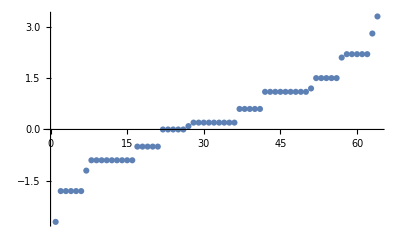

```mathematica
ListPlot[eigenval,PlotRange->All]
```

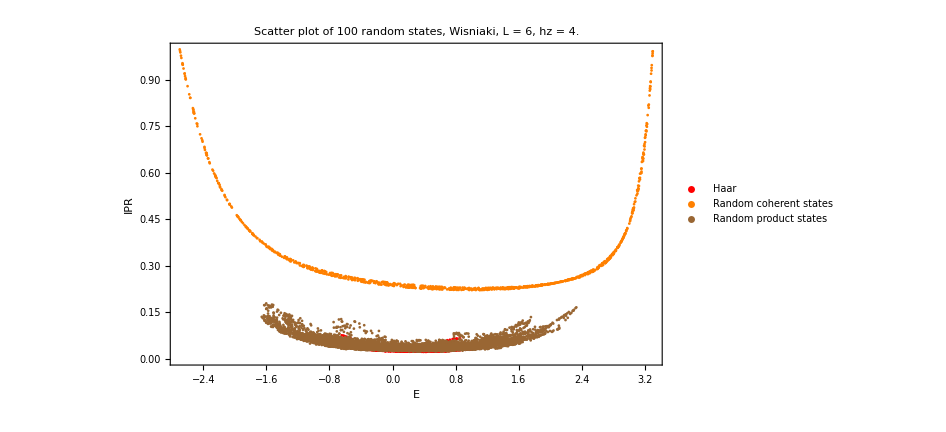

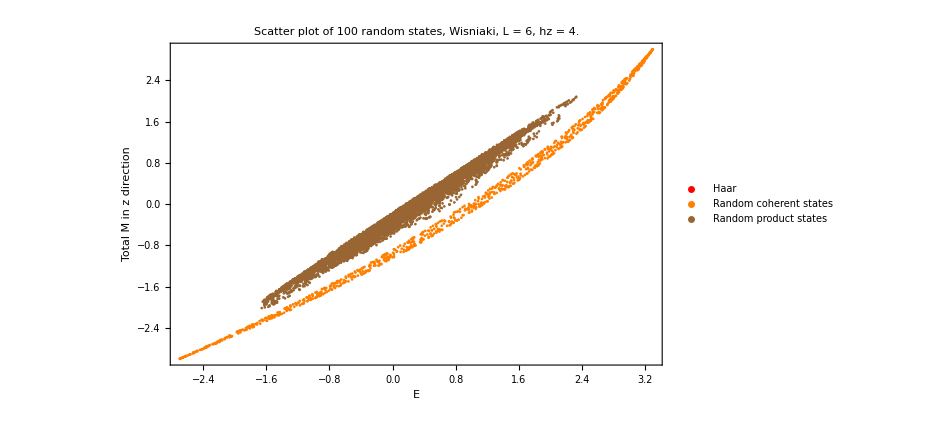

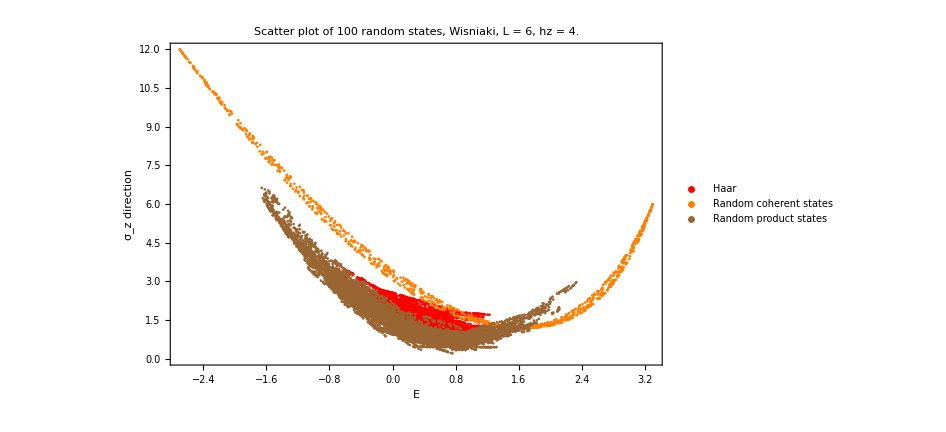

```mathematica
ListPlot[{Transpose[{energiesa,iprsa}],Transpose[{energiesb,iprsb}],Transpose[{energiesc,iprsc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["Random coherent states",Orange],Style["Random product states",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["E"],HoldForm[TraditionalForm[IPR]]}]
ListPlot[{Transpose[{energiesa,maga}],Transpose[{energiesb,magb}],Transpose[{energiesc,magc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["Random coherent states",Orange],Style["Random product states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["Total M in z direction"]}]
ListPlot[{Transpose[{energiesa,vara}],Transpose[{energiesb,varb}],Transpose[{energiesc,varc}]},PlotTheme->"Detailed",Axes->True,GridLines->None,PlotLabel->Style["Scatter plot of "<>ToString[ale]<>" random states, Wisniaki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["Random coherent states",Orange],Style["Random product states",Brown]},FrameStyle->Directive[Black,FontSize->28],FrameLabel->{Style["E"],Style["σ_z direction"]}]
```

```mathematica
tf=50.;
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
```

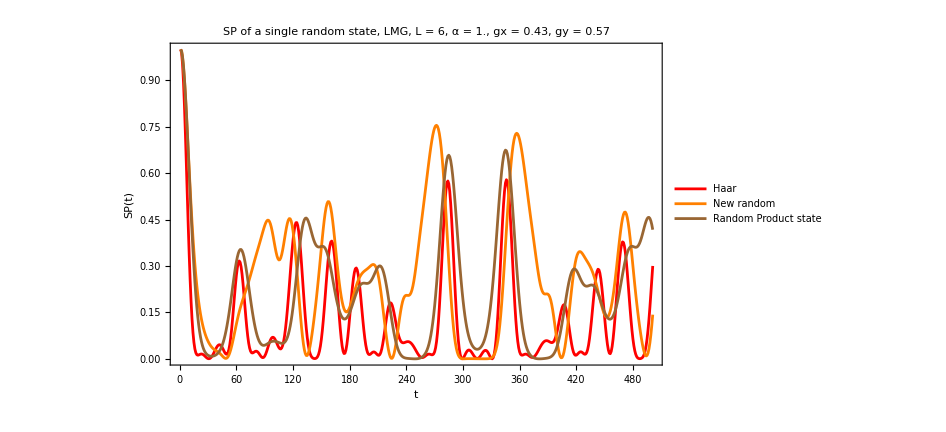

```mathematica
ListPlot[{Table[Abs[Conjugate[ψa[[1]]].i]^2,{i,ψat}],Table[Abs[Conjugate[ψb[[1]]].i]^2,{i,ψbt}],Table[Abs[Conjugate[ψc[[1]]].i]^2,{i,ψct}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["SP of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["SP(t)"]}]
```

```mathematica
densitya=ParallelTable[Dyad[i,i],{i,ψat}];
densityb=ParallelTable[Dyad[i,i],{i,ψbt}];
densityc=ParallelTable[Dyad[i,i],{i,ψct}];
reduceda=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=ParallelTable[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
```

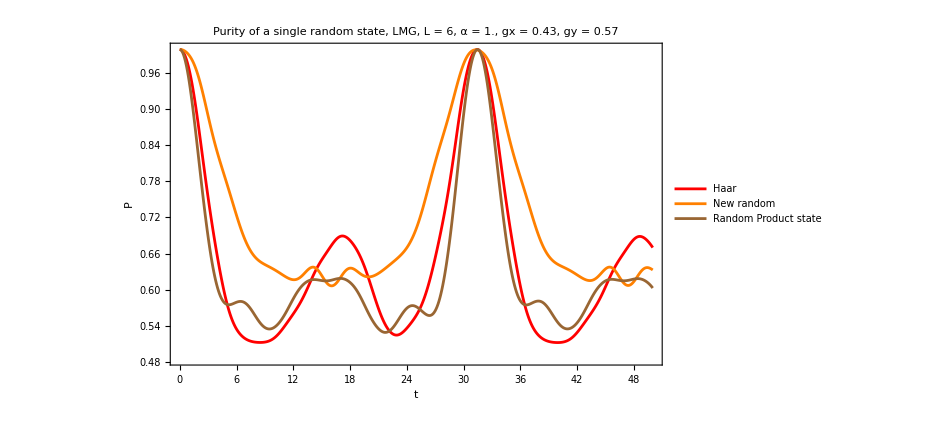

```mathematica
tlist=Range[0,tf,0.1];
ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purity of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]}]
```

```mathematica
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
```

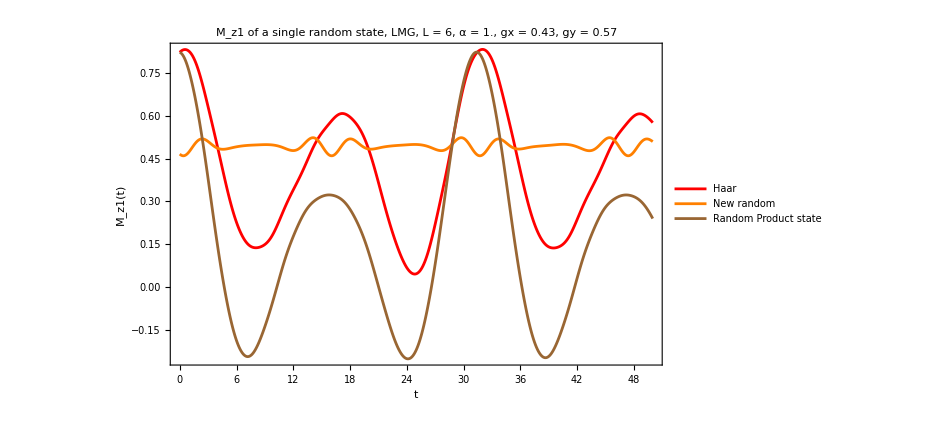

```mathematica
tlist=Range[0,tf,0.1];
ListPlot[{Transpose[{tlist,reducedmaga}],Transpose[{tlist,reducedmagb}],Transpose[{tlist,reducedmagc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, LMG, L = "<>ToString[L]<>", α = "<>ToString[α]<>", gx = "<>ToString[gx]<>", gy = "<>ToString[gy],20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,ImageSize->700,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]
```

## Quantum channel

```mathematica
α=1.;
gx=0.43;
gy=0.57;
```

```mathematica
L=5;
limit=Plot[0.25,{x,0,50.},PlotStyle->Directive[RGBColor[0.93,0.07,0.66],Dashed]];
ope=Jz[L];
ope2=KroneckerProduct[sz,IdentityMatrix[2^(L-1)]];
ale=50;
caometer=Table[haar[1],{i,ale}];
ψT={haar[L-1],Flatten[KroneckerProduct@@Table[caometer[[1]],L-1]],RandomChainProductState[L-1]};
```

```mathematica
Do[

H=Hlmg[hz,gx,gy,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H]]]]];
ψa=Table[Flatten[KroneckerProduct[i,ψT[[1]]]],{i,caometer}];
ψb=Table[Flatten[KroneckerProduct[i,ψT[[2]]]],{i,caometer}];
ψc=Table[Flatten[KroneckerProduct[i,ψT[[3]]]],{i,caometer}];
eigenψa=ParallelTable[Conjugate[eigenvec].i,{i,ψa}];
eigenψb=ParallelTable[Conjugate[eigenvec].i,{i,ψb}];
eigenψc=ParallelTable[Conjugate[eigenvec].i,{i,ψc}];
iprsa=ParallelTable[Total[Abs[i]^4],{i,eigenψa}];
iprsb=ParallelTable[Total[Abs[i]^4],{i,eigenψb}];
iprsc=ParallelTable[Total[Abs[i]^4],{i,eigenψc}];
energiesa=Table[Chop[Conjugate[i].H.i],{i,ψa}];
energiesb=Table[Chop[Conjugate[i].H.i],{i,ψb}];
energiesc=Table[Chop[Conjugate[i].H.i],{i,ψc}];
maga=Table[Chop[Conjugate[i].ope.i],{i,ψa}];
magb=Table[Chop[Conjugate[i].ope.i],{i,ψb}];
magc=Table[Chop[Conjugate[i].ope.i],{i,ψc}];
singlemaga=Table[Chop[Conjugate[i].ope2.i],{i,ψa}];
singlemagb=Table[Chop[Conjugate[i].ope2.i],{i,ψb}];
singlemagc=Table[Chop[Conjugate[i].ope2.i],{i,ψc}];
tf=50.;
ψat=Table[StateEvolution[t,ψa[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψbt=Table[StateEvolution[t,ψb[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
ψct=Table[StateEvolution[t,ψc[[1]],eigenval,eigenvec],{t,0,tf,0.1}];
densitya=Table[Dyad[i,i],{i,ψat}];
densityb=Table[Dyad[i,i],{i,ψbt}];
densityc=Table[Dyad[i,i],{i,ψct}];
reduceda=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densitya}];
reducedb=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityb}];
reducedc=Table[Chop[MatrixPartialTrace[i,2,{2,2^(L-1)}]],{i,densityc}];
puritiesa=ParallelTable[Chop[Purity[i]],{i,reduceda}];
puritiesb=ParallelTable[Chop[Purity[i]],{i,reducedb}];
puritiesc=ParallelTable[Chop[Purity[i]],{i,reducedc}];
tlist=Range[0,tf,0.1];
purityplot=ListPlot[{Transpose[{tlist,puritiesa}],Transpose[{tlist,puritiesb}],Transpose[{tlist,puritiesc}]},PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["Purities of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red,Orange,Brown},PlotRange->All,PlotLegends->{Style["Haar",Red],Style["New random",Orange],Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],HoldForm[P]},ImageSize->800];
Export["purity_Wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",purityplot];
reducedmaga=Table[Chop[Tr[sz.i]],{i,reduceda}];
reducedmagb=Table[Chop[Tr[sz.i]],{i,reducedb}];
reducedmagc=Table[Chop[Tr[sz.i]],{i,reducedc}];
styles={Style["Haar, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black],Style["New random state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black],Style["Random product state, L = "<>ToString[L]<>", hz = "<>ToString[hz],40,Black]};

(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
purities={};
directions={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
choipurities={};
choidirections={};

Do[
superOp=Superoperator[t,ψT[[i]],eigenval,eigenvec,L];

AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]];

AppendTo[choipurities,
Transpose[{t,Purity[1/2.Reshuffle[superOp]]}]];

AppendTo[choidirections,
Transpose[{t,Tr[(1/2)(KroneckerProduct[sz,sz]).Reshuffle[superOp]]}]];

,{t,0,tf,.1}];

AppendTo[listplots,
Show[{

ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","γ(Choi)"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[purities,Show[{

ListPlot[Chop[choipurities],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]

,limit}]];

AppendTo[directions,Show[{

ListPlot[Chop[choidirections],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Thick],
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->30],
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[(sz.sz).𝒟^2]]]},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->1000,PlotLabel->styles[[i]]]}]];
,{i,3}];

reducedmags={ListPlot[Transpose[{tlist,reducedmaga}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Red},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Haar",Red]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagb}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Orange},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["New random",Orange]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}],ListPlot[Transpose[{tlist,reducedmagc}],PlotTheme->"Detailed",Joined->True,Axes->True,GridLines->None,PlotLabel->Style["M_z1 of a single random state, Wisniacki, L = "<>ToString[L]<>", hz = "<>ToString[hz]<>"",20,Black],PlotStyle->{Brown},PlotRange->{{0.1,50},All},ImageSize->700,PlotLegends->{Style["Random Product state",Brown]},FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["M_z1(t)"]}]};

(*Test*)
testimage=Grid[Table[{listplots[[i]],purities[[i]],directions[[i]],reducedmags[[i]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
Export["testframe_Wisniacki_L_"<>ToString[L]<>"_hz_"<>ToString[hz]<>".png",testimage];

,{hz,-1,1,0.2}]
```